# Unit 2 Work

## Question 2.6 - Plotting Ellipses

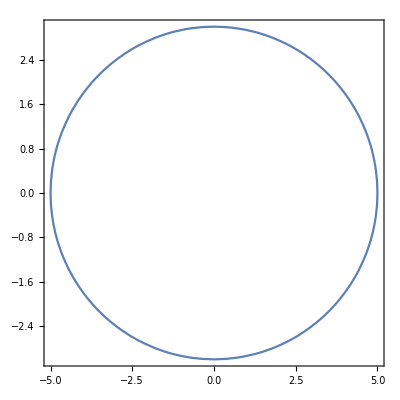

```mathematica
ContourPlot[(x^2/25)+(y^2/9)==1, {x,-5,5}, {y,-3,3}]
```

## Question 2.8 - Plots

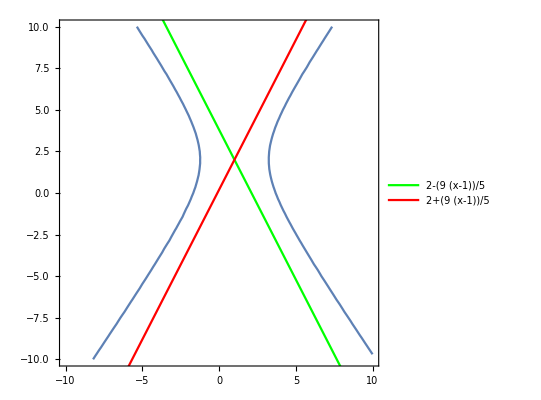

```mathematica
Show[
ContourPlot[((x-1)^2/5)-((y-2)^2/9)==1, {x, -10,10}, {y, -10,10}]
, Plot[(2- 9/5(x -1)), {x,-10,10},PlotStyle -> Directive[RGBColor[0,1,0]],PlotTheme->"Detailed"]
, Plot[(2+9/5(x-1)), {x,-10,10}, PlotStyle -> Directive[RGBColor[1,0,0]],PlotTheme->"Detailed"]
]
```

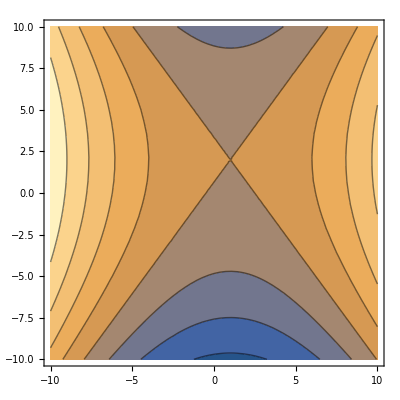

```mathematica
f :=((x-1)^2)/5 - ((y-2)^2)/9
Show[
ContourPlot[((x-1)^2)/5 - ((y-2)^2)/9, {x, -10,10}, {y, -10,10}]
]
```

## Question 2.9 - ParametricPlot

```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2π}, Frame ->True]
```

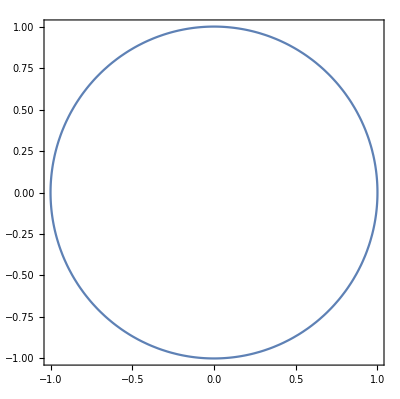

```mathematica
(*This is a test of the un/comment section*)
```

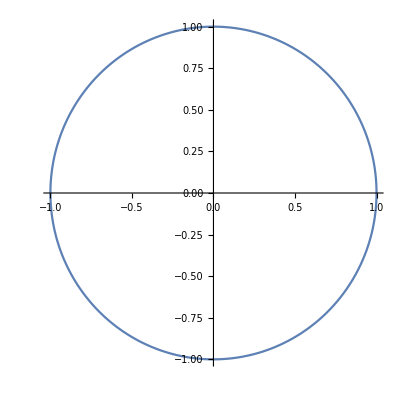

```mathematica
ParametricPlot[{Sin[t], Cos[t]}, {t,0,2π}]
```

```mathematica
ParametricPlot3D[{Cos[t], Sin[t], t}, {t, 0, 4π}]
```

-Graphics3D-

## Question 2.10 - Plot the path the curve

Plot the path traced out by the parametric curve x = 1 +
2 cost, y = 3 + 5 sin t

1+2 Cos[t]

3+5 Sin[t]

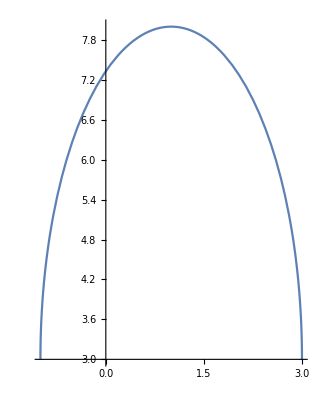

```mathematica
x = 1 + 2Cos[t]
y = 3+ 5Sin[t]
ParametricPlot[{x,y}, {t, 0, π}]
```

```mathematica
From Krisie
```

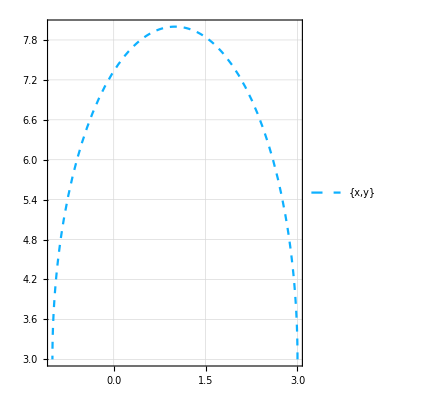

```mathematica
ParametricPlot[{x,y}, {t, 0, π}, PlotStyle ->Directive[RGBColor[0.05, 0.69,1], Dashed], PlotTheme ->"Detailed"]
```

## Question 2.16 - Derivatives

```mathematica
Clear[x,y,t,h]
```

```mathematica
x[t_]:= 3t
y[t_]:= -2t^2
x'[t]
y'[t]
```

3

-4 t

```mathematica
x''[t]
y''[t]
```

0

-4

```mathematica
D[3t, t]
```

3

```mathematica
h[t_] := 5 t^2
h''[t]
```

10

## Question 2.18 - Indefinite Integrals

#### Part 1

```mathematica
Integrate[E^4x,x]
```

```mathematica
(ⅇ^4 x^2)/2
```

```mathematica
Integrate[E[4x], x]
```

```mathematica
∫ⅇ[4 x]ⅆx
```

#### Part 2

```mathematica
Integrate[Sin[x] E^Cos[x], x]
```

-ⅇ^Cos[x]

#### Part 3

```mathematica
Integrate[x^2/(√(x^3+1)), x]
```

(2 √(1+x^3))/3

## Question 2.19 - Integration

```mathematica
Clear[x,y,t]
x[t_] := t^3
y[t_] := (3t^2)/2
Integrate[sqrt( x'[t] +  y'[t]), {t, 1,3}]
```

Hold[∫_1^3 sqrt (x'[t]+y'[t])ⅆt]

```mathematica
Integrate[Sqrt[(3t^2)^2+ (3t)^2], {t,1,3}]
```

2 √2 (-1+5 √5)